```mathematica
RootSine[n_][x_]:=Sum[Binomial[1/2,m] Sum[Binomial[m,k] (-1)^(m-k) Nest[Sin, x, k],{k,0,m}],{m,0,n}]
```

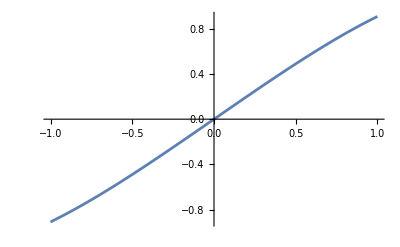

```mathematica
g=fHalf[Sin, 50];
Plot[g[x], {x, -1, 1}]
```

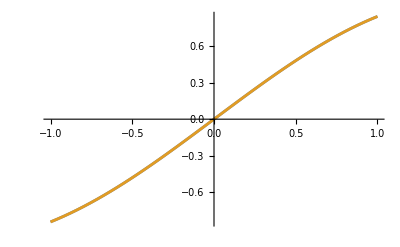

```mathematica
Plot[{Sin[x], g[g[x]]}, {x, -1, 1}]
```

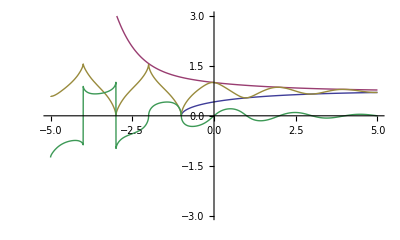

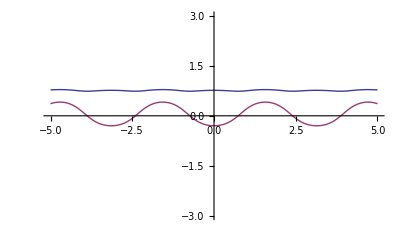

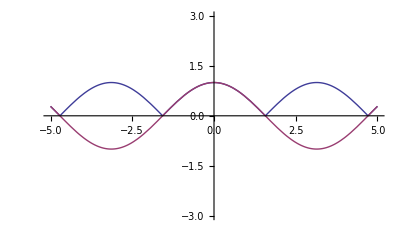

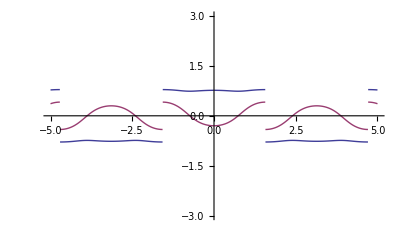

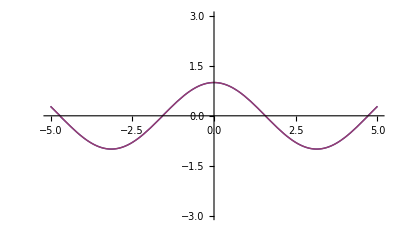

```mathematica
$PlotTheme=None;
f[x_,z_]:=If[x>=0,Nest[Cos,z,2*x],Nest[ArcCos,z,-2*x]]
n:=30
s:=15
Ni[x_,z_]:=Sum[Binomial[x+1,m]*Sum[(-1)^(k-m)*Binomial[m,k]*f[k-1,z],{k,0,m}],{m,0,n}]
Semi2[x_,z_]:=Ni[x/2,z]
Semi1[x_,z_]:=ArcCos[Semi2[x+1,z]]
FP:=Evaluate[N[FixedPoint[Cos,1.]]]
a:=21
Flow2[x_,z_]:=FP+(Semi2[x,z]-FP)*(((-1)^x+1)/2)+(Semi1[x,z]-FP)*(((-1)^(x+1)+1)/2)
FL[x_,z_]:=Nest[ArcCos,Flow2[x+a,z],a]
Plot[{Semi1[x,1],Semi2[x,1],Re[FL[x,1]],Im[FL[x,1]]},{x,-5,5},AspectRatio->Automatic,PlotRange->3]
Plot[{Re[FL[0.5,x]],Im[FL[0.5,x]]},{x,-5,5},AspectRatio->Automatic,PlotRange->3]
Plot[{Re[FL[0.5,FL[0.5,x]]],Cos[x]},{x,-5,5},AspectRatio->Automatic,PlotRange->3]
HalfCos[z_]:=If[Im[z]==0,Sign[Re[Cos[z]]]*FL[0.5,z],Sign[Re[z]]*FL[0.5,z]]
Plot[{Re[HalfCos[x]],Im[HalfCos[x]]},{x,-5,5},AspectRatio->Automatic,PlotRange->3]
Plot[{Re[HalfCos[HalfCos[x]]],Cos[x]},{x,-5,5},AspectRatio->Automatic,PlotRange->3]
```

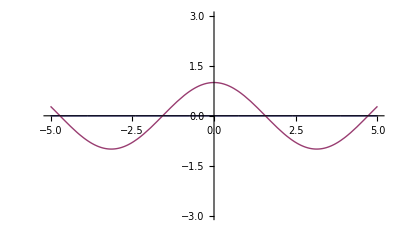

```mathematica
Plot[{Im[HalfCos[HalfCos[x]]],Cos[x]},{x,-5,5},AspectRatio->Automatic,PlotRange->3]
```

```mathematica
FindFormula[Table[{x, HalfCos[x]}, {x, -2Pi, 2Pi, 0.1}]]
```

4./((1.+24.7889^(-116.155 (-1.+#1)))^1.)&